# AntonAntonov/QuantileRegression

Quantile Regression functions

## Paclet Manifest

"Documentation"

"Diagrams"

"QuantileEnvelope-over-2D-data.png"DocumentationDiagramsQuantileEnvelope-over-2D-data.png

"QuantileRegressionFit-over-3D-data.png"DocumentationDiagramsQuantileRegressionFit-over-3D-data.png

"QuantileRegression-time-series-Atlanta-temperature.png"DocumentationDiagramsQuantileRegression-time-series-Atlanta-temperature.png

"English"

"Guides"

"Quantileregression.nb"DocumentationEnglishGuidesQuantileregression.nb

"ReferencePages"

"Symbols"

"NURBSBasis.nb"DocumentationEnglishReferencePagesSymbolsNURBSBasis.nb

"QuantileEnvelope.nb"DocumentationEnglishReferencePagesSymbolsQuantileEnvelope.nb

"QuantileEnvelopeRegion.nb"DocumentationEnglishReferencePagesSymbolsQuantileEnvelopeRegion.nb

"QuantileRegressionFit.nb"DocumentationEnglishReferencePagesSymbolsQuantileRegressionFit.nb

"QuantileRegression.nb"DocumentationEnglishReferencePagesSymbolsQuantileRegression.nb

"Tutorials"

"Kernel"

"QuantileRegression.wl"KernelQuantileRegression.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

## Web Content

### Headline Image

### Basic Description

Various Quantile Regression functions.

### Details

QuantileRegression works on time series, lists of numbers and lists of numeric pairs.

The curves computed with quantile regression are called regression quantiles.

The regression quantiles corresponding to the specified probabilities are linear combinations of B-splines generated over the specified knots.

In other words, QuantileRegression computes fits using a B-spline functions basis. The basis is specified with the knots argument and the option InterpolationOrder.

QuantileRegression takes the following options:

InterpolationOrder | 3 | interpolation order
Method | LinearProgramming | method for the quantile regression computations

QuantileRegressionFit is very similar to QuantileRegression but uses a given list of basis functions.

QuantileEnvelope provides experimental implementation of quantile envelopes points finding.

QuantileEnvelopeRegion provides experimental implementation of 2D or 3D quantile envelope region finding.

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["AntonAntonov`QuantileRegression`"];
```

### Basic Examples

Make a random signal:

```mathematica
SeedRandom[23];
n=200;
randData=Transpose[{Range[n],RandomReal[{0,100.},n]}];
```

Compute QuantileRegression with five knots for the probabilities 0.25 and 0.75:

```mathematica
qFuncs=QuantileRegression[randData,5,{0.25,0.75}];
```

Here are the formulas of the obtained regression quantiles:

```mathematica
Simplify/@Through[qFuncs[x]]
```

{Piecewise[{{0., x>200||x<1}, {3818.78-70.5999 x+0.433163 x^2-0.000875772 x^3, 801/5<x≤200}, {4099.05-75.8484 x+0.465925 x^2-0.000943942 x^3, 5 x==801}, {84.2683-0.501637 x-0.00576232 x^2+0.0000412732 x^3, 403/5<x≤602/5}, {-62.9078+4.97638 x-0.0737278 x^2+0.000322355 x^3, 204/5≤x≤403/5}, {34.9017-2.21549 x+0.102544 x^2-0.00111777 x^3, 1≤x<204/5}, {110.681-1.15976 x-0.000296216 x^2+0.0000261401 x^3, True}}],Piecewise[{{0., x>200||x<1}, {506.187-14.1371 x+0.14281 x^2-0.000456464 x^3, 403/5≤x<602/5}, {983.69-15.2439 x+0.0846418 x^2-0.000155264 x^3, 801/5<x≤200}, {59.6756+1.19519 x-0.0158668 x^2-0.0000579967 x^3, 1≤x<204/5}, {-759.529+17.4007 x-0.119132 x^2+0.000268735 x^3, 602/5≤x≤801/5}, {24.2224+3.80204 x-0.0797601 x^2+0.000464008 x^3, True}}]}

Here is a plot of the original data and the obtained regression quantiles:

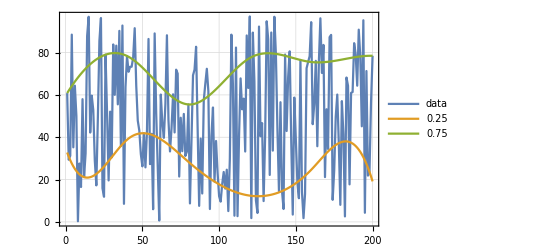

```mathematica
ListLinePlot[{randData,qFuncs[[1]]/@randData[[All,1]],qFuncs[[2]]/@randData[[All,1]]},PlotLegends->{"data",0.25,0.75},PlotStyle->{Thin,Thick,Thick},PlotTheme->"Detailed"]
```

Find the fraction of the data points that are under the second regression quantile:

```mathematica
Length[Select[randData,#[[2]]<qFuncs[[2]][#[[1]]]&]]/Length[randData]//N
```

0.75

The obtained fraction is close to the second probability, 0.75, given to QuantileRegression.

### Scope

Here is a quantile regression computation over a numerical vector:

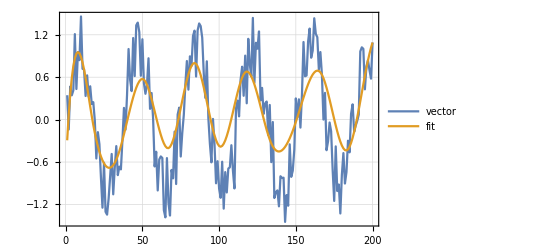

```mathematica
vecData=Sin[Range[200]/6]+RandomReal[{-0.5,0.5},200];
qFunc=First@QuantileRegression[vecData,12,0.5];
ListLinePlot[{vecData,qFunc[#]&/@Range[Length[vecData]]},PlotRange->All,PlotTheme->"Detailed",PlotLegends->{"vector","fit"}]
```

Here is a quantile regression computation over a time series object:

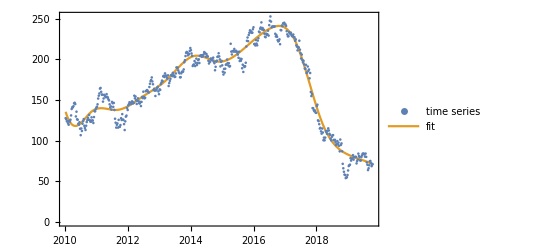

```mathematica
finData=FinancialData["GE",{{2010,1,1},{2019,10,15},"Week"}];
qFunc=First@QuantileRegression[finData,12,0.5];
DateListPlot[{finData,{#,qFunc[#]}&/@finData["Times"]},Joined->{False,True},PlotLegends->{"time series","fit"}]
```

Here we find are some randomly generated 2D points:

```mathematica
sndData=;
```

Here 2D quantile envelopes are computed of the points:

```mathematica
qs=Range[0.7,1,0.05];
qsPoints=QuantileEnvelope[sndData,qs,20];
```

Here the envelopes are plotted together with the data:

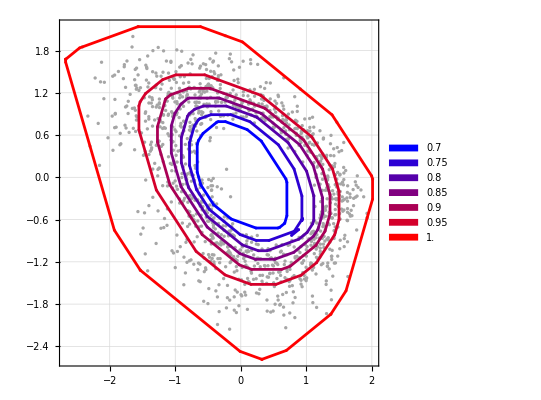

```mathematica
Block[{data=sndData},Show[{ListPlot[data,PlotStyle->{PointSize[0.006],GrayLevel[0.65]},AspectRatio->1,PlotTheme->"Detailed",PlotLegends->SwatchLegend[Blend[{Blue,Red},Rescale[#1,{Min[qs],Max[qs]},{0,1}]]&/@qs,qs]],Graphics[{PointSize[0.005],Thickness[0.005],MapThread[{Blend[{Blue,Red},Rescale[#1,{Min[qs],Max[qs]},{0,1}]],Tooltip[Line[Append[#2,#2[[1]]]],#1],Point[#2]}&,{qs,qsPoints}]}]}]]
```

## Source & Additional Information

### Creator

Anton Antonov

### Source Control Repository

https://github.com/antononcube/WL-QuantileRegression-paclet

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Fit

Linear programming

Quantile regression

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

QuantileRegression

### Original Source References and Attributions

Quantile regression through linear programming | Mathematica for prediction algorithms

Quantile regression with B-splines | Mathematica for prediction algorithms

Video: "Quantile Regression—Theory, Implementations, and Applications" presentation at WTC-2014

### Links

MathematicaForPrediction/QuantileRegression.m at master · antononcube/MathematicaForPrediction · GitHub

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

WL system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

WL built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.